```mathematica
A=208; (*Pb*)
r0=6.62;(*fm*)
a=0.546 ;(*fm*)
σ=72;(*mb, at √s=200GeV*)
ws[s_,z_]:=1/(A(1+Exp[(√(s^2+z^2)-r0)/a]));
ws1[s1_,s2_,ang_,z_]:=1/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-r0)/a]));
```

```mathematica
ρ0=1/NIntegrate[2π s ws[s,z],{s,0,∞},{z,-∞,∞}];
wsn[s_,z_]:=ρ0/(A(1+Exp[(√(s^2+z^2)-r0)/a]));
ws1n[s1_,s2_,ang_,z_]:=ρ0/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-r0)/a]));
```

```mathematica
T[s_]:=NIntegrate[wsn[s,z],{z,-∞,∞}]
T1[s1_,s2_,ang_]:=NIntegrate[ws1n[s1,s2,ang,z],{z,-∞,∞}]
```

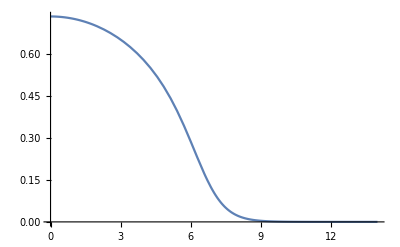

```mathematica
Plot[σ T[x],{x,0,14}]
```

```mathematica
Quiet[NIntegrate[2π x T[x],{x,0,∞}]]
```

0.999999

```mathematica
Npart[b_]:=2 A Quiet[NIntegrate[s T1[s,b,ang](1-(1-σ T[s])^A),{s,0,∞},{ang,0,2 π}]]
```

```mathematica
NpartTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NpartTab];
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
ParallelDo[NpartTab[[i,2]]=Npart[NpartTab[[i,1]]],{i,Length[NpartTab]}]//AbsoluteTiming
```

{2646.86,Null}

```mathematica
NpartTab
```

{{0.,415.09},{0.1,415.083},{0.2,415.064},{0.3,415.03},{0.4,414.983},{0.5,414.92},{0.6,414.841},{0.7,414.745},{0.8,414.629},{0.9,414.491},{1.,414.33},{1.1,414.142},{1.2,413.926},{1.3,413.676},{1.4,413.39},{1.5,413.065},{1.6,412.695},{1.7,412.277},{1.8,411.806},{1.9,411.277},{2.,410.686},{2.5,406.637},{3.,400.4},{3.5,391.658},{4.,380.359},{4.5,366.668},{5.,350.876},{5.5,333.328},{6.,314.369},{6.5,294.325},{7.,273.499},{7.5,252.166},{8.,230.578},{8.5,208.968},{9.,187.554},{9.5,166.539},{10.,146.114},{10.5,126.463},{11.,107.762},{11.5,90.1767},{12.,73.8707},{12.1,70.7768},{12.2,67.7416},{12.3,64.7662},{12.4,61.8518},{12.5,58.9999},{12.6,56.2109},{12.7,53.4866},{12.8,50.828},{12.9,48.2367},{13.,45.7123},{13.1,43.2572},{13.2,40.8721},{13.3,38.5584},{13.4,36.3161},{13.5,34.1466},{13.6,32.0506},{13.7,30.029},{13.8,28.0824},{13.9,26.2115},{14.,24.4167},{14.1,22.6983},{14.2,21.0566},{14.3,19.4917},{14.4,18.0034},{14.5,16.5914},{14.6,15.2553},{14.7,13.9943},{14.8,12.8074},{14.9,11.6935},{15.,10.6511}}

```mathematica
NpartTab={{0.,415.08987601652507},{0.1,415.0833313657752},{0.2,415.06358548242497},{0.30000000000000004,415.03025890408185},{0.4,414.982674671068},{0.5,414.9200730897662},{0.6000000000000001,414.84115854516165},{0.7000000000000001,414.74456905194353},{0.8,414.6285296715521},{0.9,414.49114589343264},{1.,414.32995726662864},{1.1,414.1423927556307},{1.2000000000000002,413.925505952458},{1.3,413.67601090315077},{1.4000000000000001,413.39035977442455},{1.5,413.0646919525468},{1.6,412.69496994630214},{1.7000000000000002,412.27681092682275},{1.8,411.80573555231445},{1.9000000000000001,411.27712254673895},{2.,410.6862734943098},{2.5,406.63744727059304},{3.,400.3999775996889},{3.5,391.657797958493},{4.,380.35870702889406},{4.5,366.667519723457},{5.,350.8764993632678},{5.5,333.3282929516488},{6.,314.36887265935167},{6.5,294.32543529196624},{7.,273.4993422587809},{7.5,252.16597193827445},{8.,230.5779535364791},{8.5,208.96843933934184},{9.,187.55418499913122},{9.5,166.53864721491618},{10.,146.11410145719276},{10.5,126.46341625912706},{11.,107.76156539360755},{11.5,90.17665995275591},{12.,73.87069211160367},{12.1,70.77683753357508},{12.2,67.74156121206272},{12.299999999999999,64.76615605199565},{12.4,61.851786669620274},{12.5,58.999920553381735},{12.6,56.210863624946874},{12.7,53.486624093380804},{12.799999999999999,50.828045946446125},{12.9,48.23665837546695},{13.,45.71228742798764},{13.1,43.257248439171164},{13.2,40.87214716935195},{13.3,38.5584032057417},{13.4,36.316099962961665},{13.5,34.14655402061447},{13.6,32.05059661290668},{13.7,30.029000077320728},{13.8,28.08243716166886},{13.9,26.21149902796103},{14.,24.416667249409937},{14.1,22.69830075005027},{14.2,21.056619654168472},{14.3,19.49168762368368},{14.4,18.003395478479327},{14.5,16.59144319955368},{14.6,15.255290761073242},{14.7,13.9942785149922},{14.8,12.807412251820402},{14.9,11.693490500167485},{15.,10.651098451259372}};
```

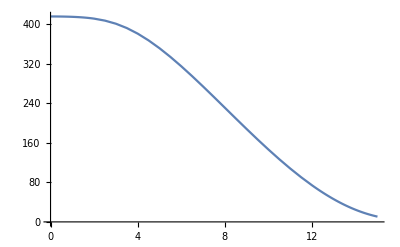

```mathematica
ListPlot[NpartTab,Joined->True]
```

```mathematica
Npartinter=Interpolation[NpartTab];
```

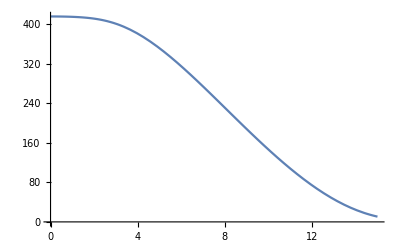

```mathematica
Plot[Npartinter[x],{x,0,15}]
```

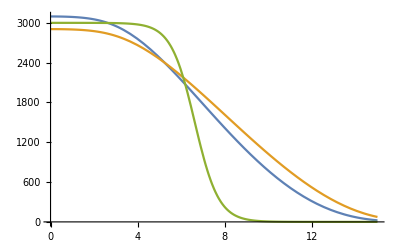

```mathematica
Plot[{Npartinter[x]^(4/3),7 Npartinter[x],3000/(1+Exp[(x-r0)/a])},{x,0,15}]
```